```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\youji\Google Drive\multi atom

```mathematica
atom=3;(*num of atoms*)
dim=2^atom;(*dimension in Hilbert space*)
(*ALT:Do[bra=ConstantArray[0,{dim,1}];ket=ConstantArray[0,{1,dim}];bra[[i,1]]=1;ket[[1,j]]=1;xij[i,j]=bra.ket,{i,1,dim},{j,1,dim}];*)
 xij[i_,j_]:=ReplacePart[ConstantArray[0,{dim,dim}],{i,j}->1]
ithzero[digit_,kth_]/;kth≤ digit:=Tuples[ReplacePart[Table[{1,0},{digit}],kth->{0}]];

(*jth=1->ith=1*)
(*n digits, kth=0(left is 1, right is n), meaning n atoms, kth in ground state*)
(*ALT: n=5;
ithzero=Compile[{{k,_Integer}},nul={};Do[nul=Append[nul,i*Boole[IntegerDigits[i,2,n][[k]]==0]],{i,0,2^n-1}],nul=Union@nul];*)
(*ALT: For[i=1,i≤ atom,i++,σ[i,1]=Sum[xij[2^atom+1-(x+2^(atom-i)+1),2^atom+1-(x+1)]*Boole[MemberQ[ithzero[atom,i],IntegerDigits[x,2,atom]]],{x,0,2^atom-1}]];*)
Do[σ[i,1]=Sum[xij[2^atom+1-(x+2^(atom-i)+1),2^atom+1-(x+1)]Boole[MemberQ[ithzero[atom,i],IntegerDigits[x,2,atom]]],{x,0,2^atom-1}],{i,1,atom}];
Do[σ[i,0]=Transpose[σ[i,1]],{i,1,atom}];
(*mapping: eeee->1111->2^4-1, i is the ith from the left*)
ρ[t_]:=Table[a[i,j][t],{i,dim},{j,dim}]
slnn=Flatten[Table[a[i,j][t],{i,dim},{j,dim}]];
(*basis:a1a2a3,a1a2b3,a1b2a3,a1b2b3,b1a2a3,b1a2b3,b1b2a3,b1b2b3*)
cij[t_]:=Table[c[i,j][t],{i,dim},{j,dim}];
slnc=Flatten[Table[c[i,j][t],{i,dim},{j,dim}]];
init=DiagonalMatrix[Append[ConstantArray[0,dim-1],1]];

(*σ[1,1]:=σ1p=({{0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}});σ[1,0]:=σ1m=({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}});σ[2,1]:=σ2p=({{0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}});σ[2,0]:=σ2m=({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0}});σ[3,1]:=σ3p=({{0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 0, 0, 0, 0}});σ[3,0]:=σ3m=({{0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0}});*)
λ0=1;k0=2Pi/λ0;
rr=0;
sh=Sinh[rr];
ch=Cosh[rr];
ΩR=0.01;
θ=Pi/2;
r[5]=1 λ0;
r[4]=0.5λ0;
r[3]=0.5λ0;
r[2]=0.25  λ0;
r[1]=-0λ0;
Λ[i_,j_]:=(*Λ[i,j]=*)0.5Sin[k0 Abs[r[i]-r[j]] ];
γ[i_,j_]:=(*γ[i,j]=*)Cos[k0 Abs[r[j]-r[i]] ];
γp[i_,j_]:=(*γp[i,j]=Cos[k0(r[i]+r[j])]*)Cos[k0(r[i])]Cos[k0(r[j])];
(*Λ[i_,j_]:=Λ[i,j]=0.5Sin[k0 Abs[r[i]-r[j]] ]KroneckerDelta[i,j];
γ[i_,j_]:=γ[i,j]=Cos[k0 Abs[r[j]-r[i]] ]KroneckerDelta[i,j];
γp[i_,j_]:=γp[i,j]=Cos[k0(r[i]+r[j])]KroneckerDelta[i,j];*)
V=0.5ΩR Sum[Exp[-I θ]Exp[-I k0 r[i]]σ[i,0]+Exp[I θ]Exp[I k0 r[i]]σ[i,1],{i,1,atom}];
SQ=-0.5sh ch Sum[γp[i,j](ρ[t].σ[i,α].σ[j,α]+σ[i,α].σ[j,α].ρ[t]-2σ[j,α].ρ[t].σ[i,α]),{i,1,atom},{j,1,atom},{α,0,1}]-0.5(sh^2+1)Sum[γ[i,j](ρ[t].σ[i,1].σ[j,0]+σ[i,1].σ[j,0].ρ[t]-2σ[j,0].ρ[t].σ[i,1]),{i,1,atom},{j,1,atom}]-0.5 sh^2Sum[γ[i,j](ρ[t].σ[i,0].σ[j,1]+σ[i,0].σ[j,1].ρ[t]-2σ[j,1].ρ[t].σ[i,0]),{i,1,atom},{j,1,atom}]-I Sum[Λ[i,j](σ[i,1].σ[j,0].ρ[t]-ρ[t].σ[i,1].σ[j,0]),{i,1,atom},{j,1,atom}];
SQc=-0.5sh ch Sum[γp[i,j]( cij[t].σ[i,α].σ[j,α]+σ[i,α].σ[j,α]. cij[t]-2σ[j,α]. cij[t].σ[i,α]),{i,1,atom},{j,1,atom},{α,0,1}]-0.5(sh^2+1)Sum[γ[i,j]( cij[t].σ[i,1].σ[j,0]+σ[i,1].σ[j,0]. cij[t]-2σ[j,0]. cij[t].σ[i,1]),{i,1,atom},{j,1,atom}]-0.5 sh^2Sum[γ[i,j]( cij[t].σ[i,0].σ[j,1]+σ[i,0].σ[j,1]. cij[t]-2σ[j,1]. cij[t].σ[i,0]),{i,1,atom},{j,1,atom}]-I Sum[Λ[i,j](σ[i,1].σ[j,0]. cij[t]- cij[t].σ[i,1].σ[j,0]),{i,1,atom},{j,1,atom}];
DR=-I (V.ρ[t]-ρ[t].V);
DRc=-I (V.cij[t]-cij[t].V);
solsq=NDSolve[{ρ'[t]==SQ+DR,ρ[0]==init},slnn,{t,0,1000}];
initc=Sum[σ[i,0],{i,1,atom}].(ρ[t]/.solsq/.t->500)[[1]];
solc=NDSolve[{cij'[t]==SQc+DRc,cij[0]==initc},slnc,{t,0,1000}];
```

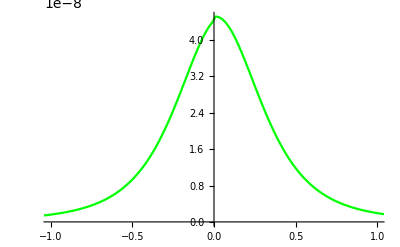

```mathematica
ss=Tr[((cij[t]/.solc)[[1]].Sum[σ[i,1],{i,1,atom}])]/.t->500;
dt=0.01;
spec=Flatten[Re[InverseFourier[Table[Tr[((cij[t]/.solc)[[1]].Sum[σ[i,1],{i,1,atom}])]-ss,{t,0,100Pi,dt}]]]];
p=IntegerPart[100Pi/dt/2];
specc=ConstantArray[0,2p];
spec=spec;
specc[[1;;p]]=spec[[p+1;;2p]];
specc[[p+1;;2p]]=spec[[1;;p]];
aaa=ListLinePlot[specc,DataRange->{-Pi 1/dt,Pi 1/dt},PlotRange->{{-1,1},Full},PlotLegends->"vac",PlotStyle->Green]
```

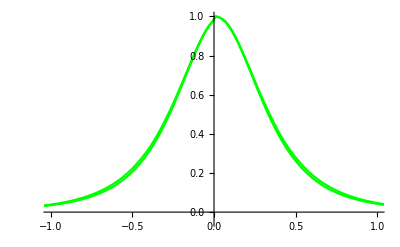

```mathematica
Show[Out[89],Out[129]]
```

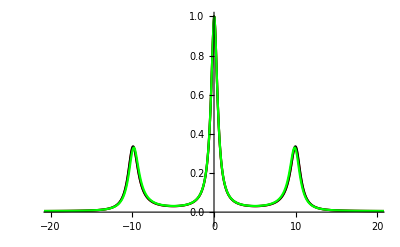

```mathematica
Show[Out[185],Out[225],Out[266]]
```

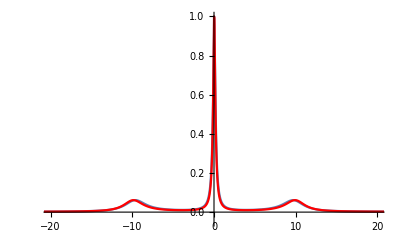

```mathematica
Show[Out[90],Out[144]]
```

```mathematica
Quit[]
```

```mathematica
atom=2;(*num of atoms*)
dim=2^atom;(*dimension in Hilbert space*)

 xij[i_,j_]:=ReplacePart[ConstantArray[0,{dim,dim}],{i,j}->1]
ithzero[digit_,kth_]/;kth≤ digit:=Tuples[ReplacePart[Table[{1,0},{digit}],kth->{0}]];

Do[σ[i,1]=Sum[xij[2^atom+1-(x+2^(atom-i)+1),2^atom+1-(x+1)]Boole[MemberQ[ithzero[atom,i],IntegerDigits[x,2,atom]]],{x,0,2^atom-1}],{i,1,atom}];
Do[σ[i,0]=Transpose[σ[i,1]],{i,1,atom}];
ρ[t_]:=Table[a[i,j][t],{i,dim},{j,dim}]
slnn=Flatten[Table[a[i,j][t],{i,dim},{j,dim}]];
cij[t_]:=Table[c[i,j][t],{i,dim},{j,dim}];
slnc=Flatten[Table[c[i,j][t],{i,dim},{j,dim}]];
init=ConstantArray[1/2^atom,{dim,dim}];

λ0=1;k0=2Pi/λ0;
rr=0.5;
sh=Sinh[rr];
ch=Cosh[rr];
Table[{n,d=n λ0;
Do[r[i]=(i-1) λ0+d,{i,1,atom}];
Λ[i_,j_]:=(*Λ[i,j]=*)0.5Sin[k0 Abs[r[i]-r[j]] ];
γ[i_,j_]:=(*γ[i,j]=*)Cos[k0 Abs[r[j]-r[i]] ];
γp[i_,j_]:=(*γp[i,j]=*)Cos[k0(r[i]+r[j])];

SQ=-0.5sh ch Sum[γp[i,j](ρ[t].σ[i,α].σ[j,α]+σ[i,α].σ[j,α].ρ[t]-2σ[j,α].ρ[t].σ[i,α]),{i,1,atom},{j,1,atom},{α,0,1}]-0.5(sh^2+1)Sum[γ[i,j](ρ[t].σ[i,1].σ[j,0]+σ[i,1].σ[j,0].ρ[t]-2σ[j,0].ρ[t].σ[i,1]),{i,1,atom},{j,1,atom}]-0.5 sh^2Sum[γ[i,j](ρ[t].σ[i,0].σ[j,1]+σ[i,0].σ[j,1].ρ[t]-2σ[j,1].ρ[t].σ[i,0]),{i,1,atom},{j,1,atom}]-I Sum[Λ[i,j](σ[i,1].σ[j,0].ρ[t]-ρ[t].σ[i,1].σ[j,0]),{i,1,atom},{j,1,atom}];
solsq=NDSolve[{ρ'[t]==SQ,ρ[0]==init},slnn,{t,0,1000},MaxSteps->50000];
solsq=NDSolve[{ρ'[t]==SQ,ρ[0]==init,WhenEvent[Re[(a[1,3][t]+a[2,4][t]+a[3,1][t]+a[4,2][t])/.solsq][[1]]==1/E,dx=1/t]},slnn,{t,0,1000},MaxSteps->50000];dx},{n,0.0,1,0.02}]
```

{{0.,0.513497},{0.02,0.523746},{0.04,0.555851},{0.06,0.612392},{0.08,0.694138},{0.1,0.798176},{0.12,0.918068},{0.14,1.04513},{0.16,1.16977},{0.18,1.28264},{0.2,1.37536},{0.22,1.44115},{0.24,1.47527},{0.26,1.47527},{0.28,1.44115},{0.3,1.37536},{0.32,1.28264},{0.34,1.16977},{0.36,1.04513},{0.38,0.918068},{0.4,0.798176},{0.42,0.694138},{0.44,0.612392},{0.46,0.555851},{0.48,0.523746},{0.5,0.513497},{0.52,0.523746},{0.54,0.555851},{0.56,0.612392},{0.58,0.694138},{0.6,0.798176},{0.62,0.918068},{0.64,1.04513},{0.66,1.16977},{0.68,1.28264},{0.7,1.37536},{0.72,1.44115},{0.74,1.47527},{0.76,1.47527},{0.78,1.44115},{0.8,1.37536},{0.82,1.28264},{0.84,1.16977},{0.86,1.04513},{0.88,0.918068},{0.9,0.798176},{0.92,0.694138},{0.94,0.612392},{0.96,0.555851},{0.98,0.523746},{1.,0.513497}}

```mathematica
Export["2xx.dat",Out[102]]
```

2xx.dat

```mathematica
Directory[]
```

C:\Users\youji\OneDrive\Documents

```mathematica
atom=2;(*num of atoms*)
dim=2^atom;(*dimension in Hilbert space*)

 xij[i_,j_]:=ReplacePart[ConstantArray[0,{dim,dim}],{i,j}->1]
ithzero[digit_,kth_]/;kth≤ digit:=Tuples[ReplacePart[Table[{1,0},{digit}],kth->{0}]];

Do[σ[i,1]=Sum[xij[2^atom+1-(x+2^(atom-i)+1),2^atom+1-(x+1)]Boole[MemberQ[ithzero[atom,i],IntegerDigits[x,2,atom]]],{x,0,2^atom-1}],{i,1,atom}];
Do[σ[i,0]=Transpose[σ[i,1]],{i,1,atom}];
ρ[t_]:=Table[a[i,j][t],{i,dim},{j,dim}]
slnn=Flatten[Table[a[i,j][t],{i,dim},{j,dim}]];
cij[t_]:=Table[c[i,j][t],{i,dim},{j,dim}];
slnc=Flatten[Table[c[i,j][t],{i,dim},{j,dim}]];
init=KroneckerProduct[{{1, -I}, {I, 1}}/2,{{1, -I}, {I, 1}}/2(*,{{1, -I}, {I, 1}}/2,{{1, -I}, {I, 1}}/2,{{1, -I}, {I, 1}}/2*)];

λ0=1;k0=2Pi/λ0;
rr=0.5;
sh=Sinh[rr];
ch=Cosh[rr];
Table[{n,d=n λ0;
(*Do[r[i]=(i-3) λ0+d,{i,1,atom}];*)
Do[r[i]=(i-1) λ0+d,{i,1,atom}];
Λ[i_,j_]:=(*Λ[i,j]=*)0.5Sin[k0 Abs[r[i]-r[j]] ];
γ[i_,j_]:=(*γ[i,j]=*)Cos[k0 Abs[r[j]-r[i]] ];
γp[i_,j_]:=(*γp[i,j]=*)Cos[k0(r[i]+r[j])];

SQ=-0.5sh ch Sum[γp[i,j](ρ[t].σ[i,α].σ[j,α]+σ[i,α].σ[j,α].ρ[t]-2σ[j,α].ρ[t].σ[i,α]),{i,1,atom},{j,1,atom},{α,0,1}]-0.5(sh^2+1)Sum[γ[i,j](ρ[t].σ[i,1].σ[j,0]+σ[i,1].σ[j,0].ρ[t]-2σ[j,0].ρ[t].σ[i,1]),{i,1,atom},{j,1,atom}]-0.5 sh^2Sum[γ[i,j](ρ[t].σ[i,0].σ[j,1]+σ[i,0].σ[j,1].ρ[t]-2σ[j,1].ρ[t].σ[i,0]),{i,1,atom},{j,1,atom}]-I Sum[Λ[i,j](σ[i,1].σ[j,0].ρ[t]-ρ[t].σ[i,1].σ[j,0]),{i,1,atom},{j,1,atom}];
solsq=NDSolve[{ρ'[t]==SQ,ρ[0]==init},slnn,{t,0,1000},MaxSteps->50000];
solsq=NDSolve[{ρ'[t]==SQ,ρ[0]==init,WhenEvent[Im[(-a[1,3][t]-a[2,4][t]+a[3,1][t]+a[4,2][t])/.solsq][[1]]==1/E,dx=1/t]},slnn,{t,0,1000},MaxSteps->50000];dx},{n,0.0,3,0.02}]
```

{{0.,1.47959},{0.02,1.46238},{0.04,1.41197},{0.06,1.33198},{0.08,1.22823},{0.1,1.10835},{0.12,0.981293},{0.14,0.856648},{0.16,0.743703},{0.18,0.650203},{0.2,0.580944},{0.22,0.536898},{0.24,0.516034},{0.26,0.516034},{0.28,0.536898},{0.3,0.580944},{0.32,0.650203},{0.34,0.743703},{0.36,0.856648},{0.38,0.981293},{0.4,1.10835},{0.42,1.22823},{0.44,1.33198},{0.46,1.41197},{0.48,1.46238},{0.5,1.47959},{0.52,1.46238},{0.54,1.41197},{0.56,1.33198},{0.58,1.22823},{0.6,1.10835},{0.62,0.981293},{0.64,0.856648},{0.66,0.743703},{0.68,0.650203},{0.7,0.580944},{0.72,0.536898},{0.74,0.516034},{0.76,0.516034},{0.78,0.536898},{0.8,0.580944},{0.82,0.650203},{0.84,0.743703},{0.86,0.856648},{0.88,0.981293},{0.9,1.10835},{0.92,1.22823},{0.94,1.33198},{0.96,1.41197},{0.98,1.46238},{1.,1.47959},{1.02,1.46238},{1.04,1.41197},{1.06,1.33198},{1.08,1.22823},{1.1,1.10835},{1.12,0.981293},{1.14,0.856648},{1.16,0.743703},{1.18,0.650203},{1.2,0.580944},{1.22,0.536898},{1.24,0.516034},{1.26,0.516034},{1.28,0.536898},{1.3,0.580944},{1.32,0.650203},{1.34,0.743703},{1.36,0.856648},{1.38,0.981293},{1.4,1.10835},{1.42,1.22823},{1.44,1.33198},{1.46,1.41197},{1.48,1.46238},{1.5,1.47959},{1.52,1.46238},{1.54,1.41197},{1.56,1.33198},{1.58,1.22823},{1.6,1.10835},{1.62,0.981293},{1.64,0.856648},{1.66,0.743703},{1.68,0.650203},{1.7,0.580944},{1.72,0.536898},{1.74,0.516034},{1.76,0.516034},{1.78,0.536898},{1.8,0.580944},{1.82,0.650203},{1.84,0.743703},{1.86,0.856648},{1.88,0.981293},{1.9,1.10835},{1.92,1.22823},{1.94,1.33198},{1.96,1.41197},{1.98,1.46238},{2.,1.47959},{2.02,1.46238},{2.04,1.41197},{2.06,1.33198},{2.08,1.22823},{2.1,1.10835},{2.12,0.981293},{2.14,0.856648},{2.16,0.743703},{2.18,0.650203},{2.2,0.580944},{2.22,0.536898},{2.24,0.516034},{2.26,0.516034},{2.28,0.536898},{2.3,0.580944},{2.32,0.650203},{2.34,0.743703},{2.36,0.856648},{2.38,0.981293},{2.4,1.10835},{2.42,1.22823},{2.44,1.33198},{2.46,1.41197},{2.48,1.46238},{2.5,1.47959},{2.52,1.46238},{2.54,1.41197},{2.56,1.33198},{2.58,1.22823},{2.6,1.10835},{2.62,0.981293},{2.64,0.856648},{2.66,0.743703},{2.68,0.650203},{2.7,0.580944},{2.72,0.536898},{2.74,0.516034},{2.76,0.516034},{2.78,0.536898},{2.8,0.580944},{2.82,0.650203},{2.84,0.743703},{2.86,0.856648},{2.88,0.981293},{2.9,1.10835},{2.92,1.22823},{2.94,1.33198},{2.96,1.41197},{2.98,1.46238},{3.,1.47959}}

```mathematica
Export["2yy.dat",Out[143]]
```

2yy.dat

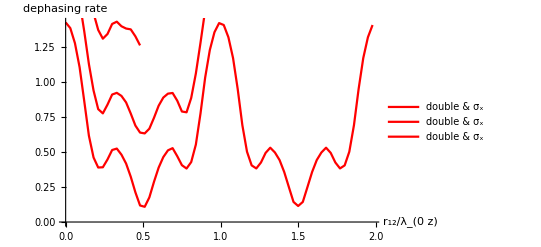

```mathematica
Show[Out[683],Out[722],Out[799]]
```

```mathematica
Tr[ρ[t].(-σ[1,0]+σ[1,1])]
```

-a[1,3][t]-a[2,4][t]+a[3,1][t]+a[4,2][t]

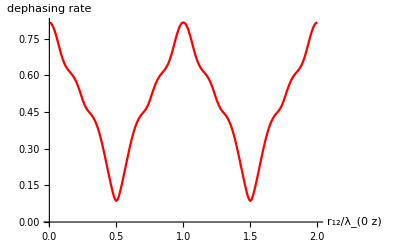

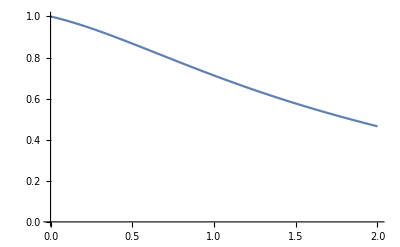

```mathematica
Out[521]
```